```mathematica
g = 9.8; (*grav constant*)
l = 0.5; (*length of pendulum*)
omega=√(g/l);
θ0 = 20*π/180; (*20 degrees*)
ω0 = 0;(*starting from rest*)

odel = {θ''[t] == -(g/l)*Sin[θ[t]],θ[0]==θ0, θ'[0]==ω0};
sol = NDSolve[odel,θ,{t,0,20}];
approx = (180/Pi)θ0 Cos[omega*t];
```

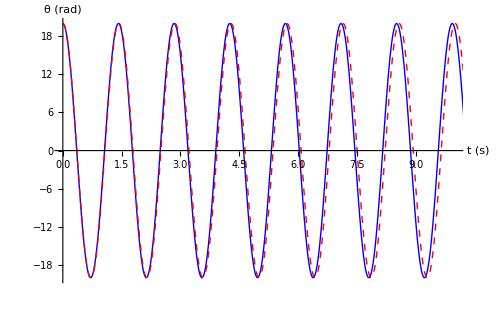

```mathematica
myPlot = Plot[{approx,(180/Pi)θ[t]/.sol},{t,0,20}, PlotStyle -> {{Blue},{Dashed,Red}}, AxesLabel ->{"t (s)", "θ  (rad)"}, PlotRange-> {{0,10},{-20,20}}, ImageSize ->{500,300}];
Show[myPlot]
```